```mathematica
string ="2020-03-05 1 0 181
2020-03-06 1 0 200
2020-03-07 2 0 241
2020-03-08 3 0 241
2020-03-09 7 0 241
2020-03-10 7 0 241
2020-03-11 13 0 645
2020-03-12 16 0 848
2020-03-13 24 0 924
2020-03-14 38 0 1017
2020-03-15 61 0 1476
2020-03-16 62 0 2405
2020-03-17 85 0 2911
2020-03-18 116 0 3070
2020-03-19 150 0 4832
2020-03-20 202 0 6438
2020-03-21 240 0 7425
2020-03-22 274 0 9315
2020-03-23 402 0 12815
2020-03-24 554 0 15529
2020-03-25 709 0 15529
2020-03-26 927 0 20471
2020-03-27 1170 1 28537
2020-03-28 1187 1 31963
2020-03-29 1280 2 35539
2020-03-30 1326 3 38409
2020-03-31 1353 5 41072
2020-04-01 1380 5 44292
2020-04-02 1462 7 47956
2020-04-03 1505 7 50361
2020-04-04 1585 9 53937
2020-04-05 1655 11 56873
2020-04-06 1686 12 58098
2020-04-07 1749 13 58098
2020-04-08 1845 18 63776
2020-04-09 1935 18 68874 
2020-04-10 2003 24 73028
2020-04-11 2028 25 75053
2020-04-12 2173 25 80085
2020-04-13 2272 27 83663
2020-04-14 2415 27 87022
2020-04-15 2506 44 90515
2020-04-16 2605 48 95060
2020-04-17 2783 50 100827
2020-04-18 3034 52 108021
2020-04-19 3158 54 114711
2020-04-20 3300 58 121510
2020-04-21 3465 58 126937";
data = ImportString[string, "Table"]
```

{{2020-03-05,1,0,181},{2020-03-06,1,0,200},{2020-03-07,2,0,241},{2020-03-08,3,0,241},{2020-03-09,7,0,241},{2020-03-10,7,0,241},{2020-03-11,13,0,645},{2020-03-12,16,0,848},{2020-03-13,24,0,924},{2020-03-14,38,0,1017},{2020-03-15,61,0,1476},{2020-03-16,62,0,2405},{2020-03-17,85,0,2911},{2020-03-18,116,0,3070},{2020-03-19,150,0,4832},{2020-03-20,202,0,6438},{2020-03-21,240,0,7425},{2020-03-22,274,0,9315},{2020-03-23,402,0,12815},{2020-03-24,554,0,15529},{2020-03-25,709,0,15529},{2020-03-26,927,0,20471},{2020-03-27,1170,1,28537},{2020-03-28,1187,1,31963},{2020-03-29,1280,2,35539},{2020-03-30,1326,3,38409},{2020-03-31,1353,5,41072},{2020-04-01,1380,5,44292},{2020-04-02,1462,7,47956},{2020-04-03,1505,7,50361},{2020-04-04,1585,9,53937},{2020-04-05,1655,11,56873},{2020-04-06,1686,12,58098},{2020-04-07,1749,13,58098},{2020-04-08,1845,18,63776},{2020-04-09,1935,18,68874},{2020-04-10,2003,24,73028},{2020-04-11,2028,25,75053},{2020-04-12,2173,25,80085},{2020-04-13,2272,27,83663},{2020-04-14,2415,27,87022},{2020-04-15,2506,44,90515},{2020-04-16,2605,48,95060},{2020-04-17,2783,50,100827},{2020-04-18,3034,52,108021},{2020-04-19,3158,54,114711},{2020-04-20,3300,58,121510},{2020-04-21,3465,58,126937}}

```mathematica
outputfolder ="C:\\Users\\fskdm\\Projects\\sa-coronavirus-2020\\";
exportfile =DateString[{outputfolder,"Year", "_", "Month", "_", "Day", "_SA_COVID-19.CSV"}];
CopyToClipboard[exportfile]
Export[exportfile,{{"Date",  "Cumulative cases", "Deaths", "Tests"}}~Join~data]
```

C:\Users\fskdm\Projects\sa-coronavirus-2020\2020_04_21_SA_COVID-19.CSV

```mathematica
Length[data]
```

46

```mathematica
eventstring = "2020-03-9\t5\t-100\tFS Church meeting 
2020-03-15\t11\t-100\tState of Disaster
2020-03-26\t22\t-100\tLockdown";
eventdata = ImportString[eventstring, "TSV"];
eventTseries = TimeSeries[eventdata[[All, {1,3}]]];
casesTseries = TimeSeries[data[[All, {1,2}]]];
deathsTseries = TimeSeries[data[[All, {1,3}]]];
testsTseries = TimeSeries[data[[All, {1,4}]]];
```

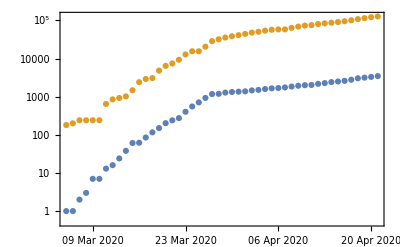

```mathematica
DateListPlot[{casesTseries, testsTseries, Map[Callout[#[[{1,3}]],#[[4]]]&, eventdata]}, DateTicksFormat->{"Day", " ", "MonthNameShort", " ", "Year"}, ScalingFunctions->"Log", Joined->False]
```

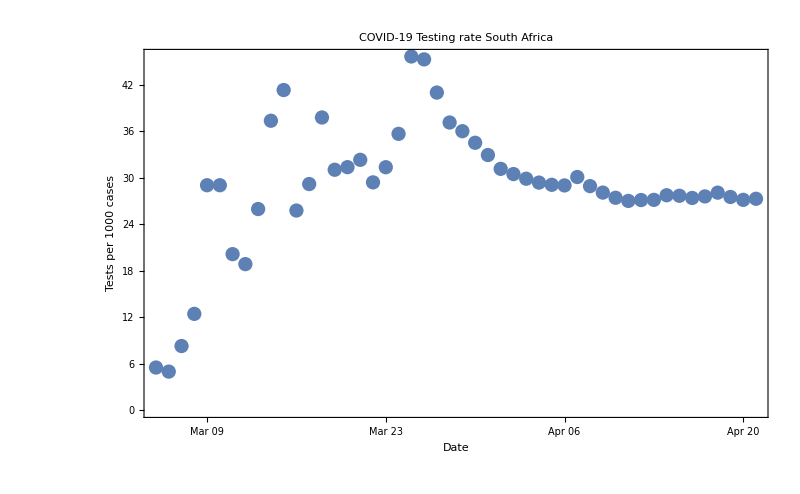

```mathematica
testrateplot =DateListPlot[Transpose[Join[{data[[All,1]]},{data[[All,2]]/data[[All,4]]*1000}]]
, Frame->True
, FrameLabel->{"Date","Tests per 1000 cases"}
, FrameStyle-> Directive[Black, Medium]
, PlotLabel->Style["COVID-19 Testing rate\nSouth Africa", Large, Black]
, ImageSize->800
, Joined->False
]
```

```mathematica
outputfolder ="C:\\Users\\fskdm\\Projects\\sa-coronavirus-2020\\";
exportfile =DateString[{outputfolder,"Year", "_", "Month", "_", "Day", "_Test_Rate.png"}];
CopyToClipboard[exportfile]
Export[exportfile,testrateplot]
```

C:\Users\fskdm\Projects\sa-coronavirus-2020\2020_04_20_Test_Rate.png

```mathematica
eqn =  a Exp[b x];
model = FindFit[casesTseries["Values"][[1;;23]], eqn, {a,b}, x]
```

{a→2.72183,b→0.264192}

```mathematica
eqn /.model
```

2.72183 ⅇ^(0.264192 x)

```mathematica
bmodel = FindFit[casesTseries["Values"][[24;;]], eqn, {a,b}, x]
```

{a→1083.02,b→0.0455446}

```mathematica
bdouble =Solve[((eqn /. bmodel)/.x-> (60))*2 ==(eqn /. bmodel)/.x-> (60+d), d]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{d→15.2191}}

```mathematica
double =Solve[((eqn /. model)/.x-> (60))*2 ==(eqn /. model)/.x-> (60+d), d]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{d→2.62365}}

```mathematica
lineqn =a + b x;
linmodel = FindFit[casesTseries["Values"][[24;;]], lineqn, {a,b}, x]
```

{a→897.29,b→90.0238}

```mathematica
exportgraphic =Show[
ListPlot[{
casesTseries["Values"]
,Table[eqn /. model, {x, 1, 25}]
,Table[Missing[],23]~Join~Table[eqn /. bmodel, {x,1,  Length[casesTseries["Values"]]-23}]
,Table[Missing[],23]~Join~Table[lineqn /. linmodel, {x,1,  Length[casesTseries["Values"]]-23}]
, deathsTseries["Values"]
,Map[Callout[#[[{2,3}]],#[[4]], Below]&, eventdata]
}
, Frame->True
, FrameStyle->Black
, FrameLabel->{"Days since 4 March 2020", "Cases"}
, AxesStyle->Directive[Black, Bold, Medium]
, PlotLabel-> Style["COVID-19 Cases\nSouth Africa: "<>DateString[{"Day", " ", "MonthName", " ", "Year"}], Bold,Large]
, PlotTheme->"Default"
, PlotRange->{All, {-300, All}}
, Joined->{False,True, True,True, False, False}
, PlotLegends->{"Cases", "Exponential fit", "Exponential fit","Linear fit", "Deaths","Events"}
, Filling->{6 -> Axis}
, FillingStyle->Directive[Thickness[.01]]
]
, Graphics[Text[
Column[
{Style["Officially confirmed cases", Black, Medium]
, Style["Doubling time: "<>ToString[NumberForm[First[d /. double], 3]]<>" days", Orange, Medium]
, Style["Doubling time: "<>ToString[NumberForm[First[d /. bdouble], 3]]<>" days", Green, Medium]
, Style["Data Sources: sacoronavirus.co.za, \nwww.gov.za/speeches"]
}
]
, {1,1500}, {-1,0}]
]
, ImageSize->800
(*,ImagePadding->{{Automatic,100},{Automatic,Automatic}} *)
]
```

-Graphics-

```mathematica
outputfolder ="C:\\Users\\fskdm\\Projects\\sa-coronavirus-2020\\";
exportfile =DateString[{outputfolder,"Year", "_", "Month", "_", "Day", "_FB.png"}];
CopyToClipboard[exportfile]
Export[exportfile,exportgraphic]
```

C:\Users\fskdm\Projects\sa-coronavirus-2020\2020_04_21_FB.png

```mathematica
Reduce[( eqn /. model~Join~{x-> 6} )== 2 (eqn /. model), x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&x==3.48247 (1.02977+(0.+6.28319 ⅈ) C[1])

```mathematica
( eqn /. model )== 2 (eqn /. model)
```

2.04679 ⅇ^(0.287152 x)==4.09358 ⅇ^(0.287152 x)

```mathematica
( eqn /. model~Join~{x-> 2} )== 2 (eqn /. model)
```

3.63488==4.09358 ⅇ^(0.287152 x)

```mathematica
((eqn /. model)/.x-> (60))*2
```

2.4533×10^7

```mathematica
(eqn /. model)/.x-> (60+d)/.double
```

{2.4533×10^7}

```mathematica
double =Solve[((eqn /. model)/.x-> (10))*2 ==(eqn /. model)/.x-> (10+d), d]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{d→2.56214}}

```mathematica
Log[eqn]//Simplify
```

Log[a ⅇ^(b x)]

```mathematica
Log[2.]/Log[200]*16.
```

2.09318

```mathematica
0.6931471805599453
```

```mathematica
12815/60.
```

213.583

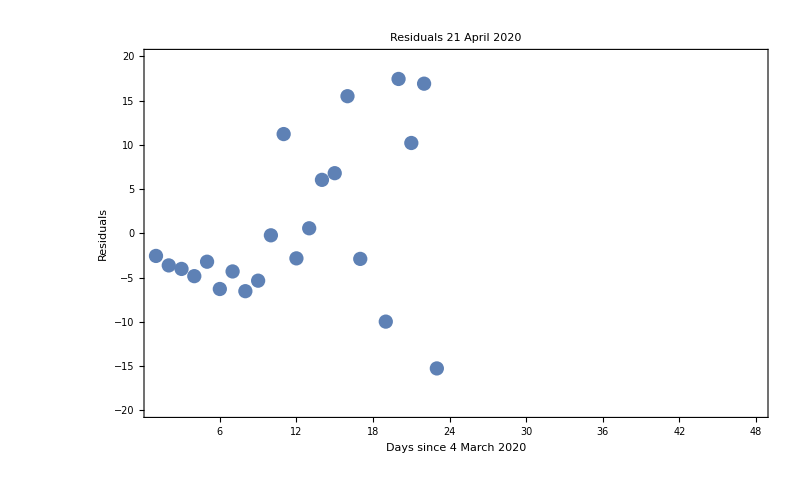

```mathematica
ListPlot[{casesTseries["Values"]-Table[eqn /. model, {x, 1,  Length[casesTseries["Values"]]}]}

, AxesStyle->Directive[Black, Bold, Medium]
, PlotLabel-> Style["Residuals\n"<>DateString[{"Day", " ", "MonthName", " ", "Year"}], Bold,Large]
, PlotTheme->"Default"
, PlotRange->{All, {-20,20}}
, Joined->{False,False, True}
, Frame->True
, FrameLabel->{"Days since 4 March 2020","Residuals"}
, ImageSize->800
]
```

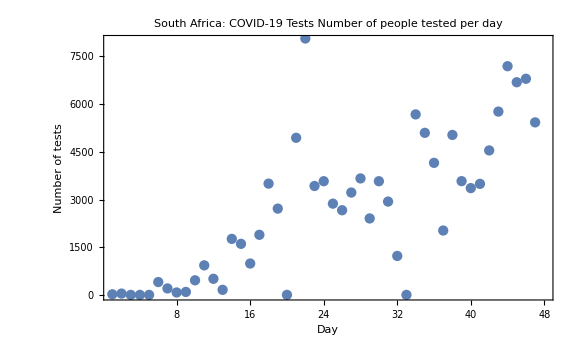

```mathematica
ListPlot[N[RotateLeft[ data[[All,4]]]-data[[All, 4]]]
	, Frame->True
	, FrameLabel->{"Day", "Number of tests"}
	, PlotLabel -> "South Africa: COVID-19 Tests\nNumber of people tested per day"
	, PlotRange->{All, {0,8000}}
	, ImageSize->Large
]
```

```mathematica
Log[N[data[[All,2]]]]
```

{0.,0.,0.693147,1.09861,1.94591,1.94591,2.56495,2.77259,3.17805,3.63759,4.11087,4.12713,4.44265,4.75359,5.01064,5.30827,5.48064,5.61313,5.99645,6.31716,6.56386,6.83195,7.06476,7.07918,7.15462,7.18992,7.21008,7.22984,7.28756,7.31655,7.36834,7.41156,7.43011,7.4668,7.52023,7.56786,7.6024,7.61481,7.68386,7.72842,7.78945,7.82644,7.86519,7.93128,8.01764}

```mathematica
logdata = Transpose[Join[{N[data[[All,2]]]}, { N[RotateLeft[ data[[All,2]]]-data[[All, 2]]]}]]
```

{{1.,0.},{1.,1.},{2.,1.},{3.,4.},{7.,0.},{7.,6.},{13.,3.},{16.,8.},{24.,14.},{38.,23.},{61.,1.},{62.,23.},{85.,31.},{116.,34.},{150.,52.},{202.,38.},{240.,34.},{274.,128.},{402.,152.},{554.,155.},{709.,218.},{927.,243.},{1170.,17.},{1187.,93.},{1280.,46.},{1326.,27.},{1353.,27.},{1380.,82.},{1462.,43.},{1505.,80.},{1585.,70.},{1655.,31.},{1686.,63.},{1749.,96.},{1845.,90.},{1935.,68.},{2003.,25.},{2028.,145.},{2173.,99.},{2272.,143.},{2415.,91.},{2506.,99.},{2605.,178.},{2783.,251.},{3034.,124.},{3158.,142.},{3300.,165.},{3465.,-3464.}}

```mathematica
brplot =ListLogLogPlot[logdata, Frame->True, FrameLabel->{"Cumulative cases","New cases"}, Joined->True, PlotMarkers->"+", PlotLabel->"Bhatia-Reich plot\nConfirmed COVID-19 Cases, South Africa", ImageSize->Large]
```

-Graphics-

```mathematica
exportfile =DateString[{outputfolder,"Year", "_", "Month", "_", "Day", "_BRplot.png"}];
CopyToClipboard[exportfile];
Export[exportfile, brplot]
```

C:\Users\fskdm\Projects\sa-coronavirus-2020\2020_04_20_BRplot.png

```mathematica
casesperthousand = N[data[[-1,2]]/data[[-1,4]]*1000,3];
reportstring=ToString[data[[-1,4]]]<> " tests were conducted to confirm " <> ToString[data[[-1,2]]] <> " cases. This is a testing rate of " <> ToString[casesperthousand] <> " cases per thousand tests.";
CopyToClipboard[reportstring];
Print[reportstring]
```

126937 tests were conducted to confirm 3465 cases. This is a testing rate of 27.3 cases per thousand tests.